## Singularities and Laurent Series of Error Function

```mathematica
Series[Erf[z+1/z],{z,1,10}]
```

Erf[2]+(2 (z-1)^2)/(ⅇ^4 √π)-(2 (z-1)^3)/(ⅇ^4 √π)-(2 (z-1)^4)/(ⅇ^4 √π)+(6 (z-1)^5)/(ⅇ^4 √π)-(16 (z-1)^6)/(3 (ⅇ^4 √π))+(20 (z-1)^8)/(3 ⅇ^4 √π)-(34 (z-1)^9)/(3 (ⅇ^4 √π))+(179 (z-1)^10)/(15 ⅇ^4 √π)+O[z-1]^11

```mathematica
Series[Erf[1/z],{z,0,10}]
```

(-1)^Floor[(π+2 Arg[z])/(2 π)]+ⅇ^(-1/z^2) (-z/(√π)+z^3/(2 √π)-(3 z^5)/(4 √π)+(15 z^7)/(8 √π)-(105 z^9)/(16 √π)+O[z]^11)

## The Black Scholes Pricing Formula

```mathematica
normalCDF[d_]:=1/2(1+Erf[d/(√2)]);
lo[S_,K_,T_,r_]:= Log[S/K]+r*T;
Z[σ_,T_]:= σ √T;
d1[lo_,Z_]:=lo/Z+Z/2;
d2[lo_,Z_]:=lo/Z-Z/2;
BSCall[S_,lo_,Z_]:=S(normalCDF[d1[lo,Z]]-Exp[-lo]normalCDF[d2[lo,Z]]);
BSCallHandy[S_,K_,T_,r_,σ_]:=BSCall[S,lo[S,K,T,r],Z[σ,T]];
BSPut[S_,lo_,Z_]:=S(-normalCDF[-d1[lo,Z]]+Exp[-lo]normalCDF[-d2[lo,Z]]);
BSPutHandy[S_,K_,T_,r_,σ_]:=BSPut[S,lo[S,K,T,r],Z[σ,T]];
```

## The Lewis Fourier Pricing Formula for Black Scholes Model

### Basic Functions

```mathematica
chf[u_,μ_,σ_]:=Exp[I u μ -(u^2 σ^2)/2]; 
chf2[u_,S_,K_,T_,r_,σ_]:=Exp[I u ((r- 1/2 σ^2) T + Log[S/K])-(u^2 σ^2 T)/2]; 
FC[k_,α_]:= 1/(-I k - α) - 1/(-I k - α + 1);
```

### Call Option Formula

```mathematica
LewisCall[S_,K_,T_,r_,σ_,α_,b_]:= (Exp[- r T] K)/π ∫_0^b Re[chf2[k-I α,S,K,T,r,σ] FC[k,α]]ⅆk;
```

### Implementation and Comparison

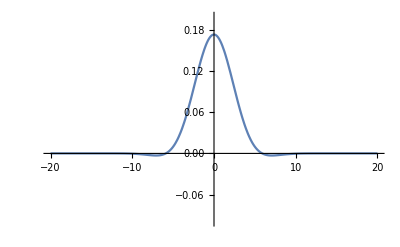

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3,α=6,b=10},
Plot[Re[chf2[k-I α,S,K,T,r,σ] FC[k,α]],{k,-20,20},PlotRange->{{-20,20},{-0.1,0.2}}]
]
```

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3,α=5,b},
Table[{LewisCall[S,K,T,r,σ,α,b]//N,
BSCallHandy[S,K,T,r,σ]},{b,10,15,1}]
]
```

{{14.2375,14.2313},{14.2335,14.2313},{14.2319,14.2313},{14.2314,14.2313},{14.2313,14.2313},{14.2313,14.2313}}

## The Lewis Fourier Pricing Formula for Heston-Nandi Model